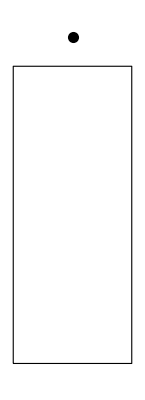

```mathematica
Graphics[{
{EdgeForm[Thick],FaceForm[None],Rectangle[{0,0},{8,20}]},
{PointSize[0.02],Point[{4,22}]}
}]
```

```mathematica
RevolutionPlot3D[√(1-θ^2),{θ,0,1}]
```

-Graphics3D-

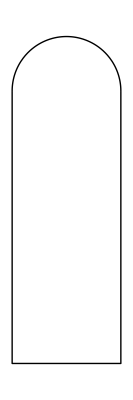
-Graphics3D- | -Graphics-

```mathematica
Module[{r,d,H,h,p1,p2},
r=4;
d:=2*r;

h=20;
H:=h+r;

p1:=Show[
Graphics3D[Cylinder[{{0,0,0},{0,0,h}},r]],
RevolutionPlot3D[√(r^2-x^2)+h,{x,0,r},PlotStyle->White,Mesh->None],
ViewPoint->Front,
Boxed->False,
PlotRange->{0,H},
PlotRangePadding->0.1];

p2:=Show[
Graphics[{Thick,Line[{{-r,h},{-r,0},{r,0},{r,h}}]}],
Plot[√(r^2-x^2)+h,{x,-r,r},PlotStyle->{Thick,Black}],
PlotRange->{0,H},
PlotRangePadding->0.1];

Grid[{{p1,p2}}]
]
```

```mathematica
Integrate[π*(r^2-x^2),{x,0,r}]
```

(2 π r^3)/3

```mathematica
Manipulate[
Module[{Vcan,h,V,r,H,hL1},
Vcan=0.375;(*L*)
h=20;(*cm*)

V[rad_,height_]:=π*rad^2*height+(2*π)/3*rad^3;

r:=rad/.First@Solve[Vcan*1000==V[rad,h]∧rad>0,rad];
H:=h+r;

hL1:=height/.Solve[f*Vcan*1000==V[r,height],height];
r

],
Control[{{f,0.75,""},0,1,0.01,Appearance->"Labeled"}]
]
```

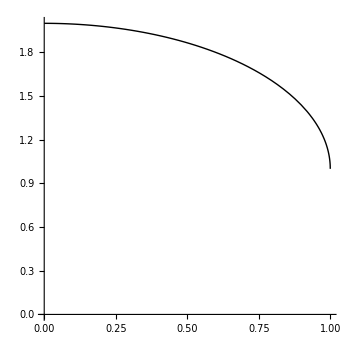
-Graphics- | -Graphics3D-

```mathematica
Module[{r,h,y,opt,p1,p2},
r=1;
h=1;
y[x_]:=√(r^2-x^2)+h;

opt:=Sequence[PlotRangePadding->0.1,ImageSize->350,AspectRatio->1];
p1:=Plot[y[x],{x,0,r},PlotStyle->{Thick,Black},PlotRange->{{0,r},{0,r+h}},Evaluate@opt];
p2:=RevolutionPlot3D[y[x],{x,0,r},Mesh->None,ViewPoint->Front,PlotRange->{{-r,r},{-r,r},{0,r+h}},Evaluate@opt];

Grid[{{p1,p2}}]
]
```

```mathematica
Manipulate[
Module[{Vcan,h,V,r,H,vL,hL},
Vcan=0.375;(*L*)
h=2.0;(*dm*)

V[rad_,h1_,h2_]:=π*rad^2*h1+If[h2==0,0,π/6*h2*(3*rad^2+3*h2^2/Tan[ArcSin[h2/rad]]^2+h2^2)];
r:=rad/.First@Solve[Vcan==V[rad,h,rad]∧rad>0,rad];
H:=h+r;

vL:=f*Vcan;

(*hL:=If[vL<V[r,h,0],h1/.Solve[vL==V[r,h1,0],h1],(*h+*)h2/.Solve[vL==V[r,h,h2](*∧(0≤h2≤r)*),h2]];*)

hL:=If[vL<V[r,h,0],h1/.First@Solve[vL==V[r,h1,0],h1],h+Re[h2/.Solve[vL==V[r,h,h2],h2][[2]]]];

Show[
Plot[{Evaluate[√(r^2-x^2)+h],Evaluate[√(r^2-x^2)+h]},{x,-r,r},PlotStyle->{{Thick,Black}},Filling->{1->{0,Blue},2->{hL,White}}],
Graphics[{
{Thick,Line[{{-r,h},{-r,0},{r,0},{r,h}}]}
}],
PlotRange->{{-r,1.2*r},{0,H}},PlotRangePadding->0.01,ImageSize->{150,300},Axes->False,AspectRatio->Full]
],
Control[{{f,0.75,""},0,1,0.01,Appearance->"Labeled"}]
]
```

```mathematica
Module[{y},
y[x1_,x2_]:=x1+x2/Tan[x2];
y[1,0]
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate